# Chapter 2

## Example 2.1

```mathematica
Remove["Global`*"]
```

```mathematica
eq1=m1*g-T==-m1*a;
eq2=m2*g-T==m2*a;
```

```mathematica
Solve[{eq1,eq2},{a,T}]
```

{{a→-(g m1-g m2)/(m1+m2),T→(2 g m1 m2)/(m1+m2)}}

## Example 2.3

```mathematica
Remove["Global`*"]
```

```mathematica
SetOptions[Plot,Frame->True,Axes-> False,BaseStyle->{FontSize->16}];
```

```mathematica
ODEsolution = DSolve[{m*x''[t]== c/(t^2 + b^2), x[0] == 0,
x'[0] == 0}, x[t], t];
```

```mathematica
position = x[t] /. ODEsolution[[1]]
```

(c (2 t ArcTan[t/b]+b Log[b^2]-b Log[b^2+t^2]))/(2 b m)

```mathematica
velocity = D[position, {t}]
```

(c (-(2 b t)/(b^2+t^2)+(2 t)/(b (1+t^2/b^2))+2 ArcTan[t/b]))/(2 b m)

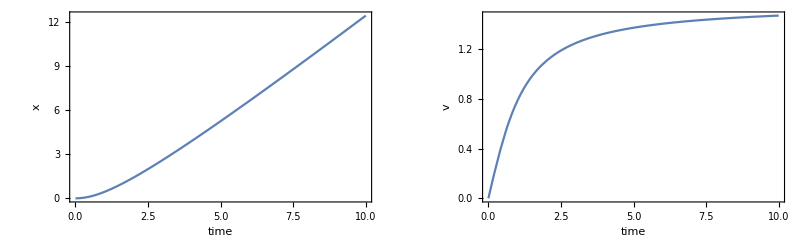

```mathematica
c = 1; m = 1; b=1;
GraphicsGrid[{{Plot[position, {t, 0, 10},FrameLabel -> {"time", "x"}],
 Plot[velocity, {t, 0, 10} ,FrameLabel -> {"time", "v"}]}}]
```

## Example 2.4

```mathematica
Remove["Global`*"]
```

```mathematica
SetOptions[Plot,Frame->True,Axes-> False,BaseStyle->{FontSize->16},
PlotRange->All];
```

```mathematica
ODEsolution = DSolve[{m x''[t]==-b x'[t],x[0]==xo,x'[0]==vo},x[t],t];
```

```mathematica
position=Collect[x[t]/.ODEsolution[[1]],{v0,m}]
```

(ⅇ^(-(b t)/m) m (-vo+ⅇ^((b t)/m) vo))/b+xo

```mathematica
velocity=D[position,t]
```

vo-ⅇ^(-(b t)/m) (-vo+ⅇ^((b t)/m) vo)

```mathematica
vo=1; xo=0; m=1; b=1;
```

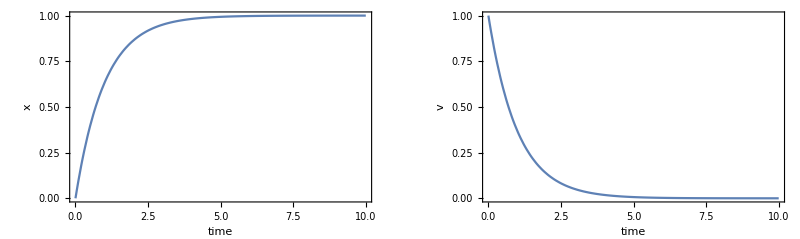

```mathematica
GraphicsGrid[{{Plot[position,{t,0,10},FrameLabel->{"time","x"}],
Plot[velocity,{t,0,10},FrameLabel->{"time","v"}]}}]
```

## Example 2.6

```mathematica
Remove["Global`*"]
```

```mathematica
SetOptions[Plot,Frame->True,Axes-> False,BaseStyle->{FontSize->16},PlotRange->All];
```

```mathematica
integral=Assuming[(vf>0)&&(vt>0)&&(vf<vt),Integrate[1/(vt^2 -  v^2),{v,0,vf}]]
```

ArcTanh[vf/vt]/vt

```mathematica
velocity=vt Tanh[(c t vt)/m]
```

vt Tanh[(c t vt)/m]

```mathematica
position=Integrate[velocity,t]
```

(m Log[Cosh[(c t vt)/m]])/c

```mathematica
m=1; g=9.8; c=0.2;vt=Sqrt[m g/c];
```

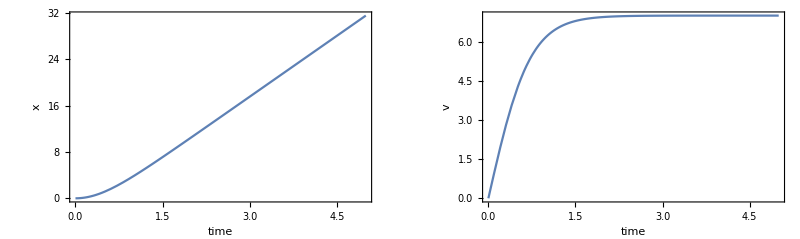

```mathematica
GraphicsGrid[{{Plot[position,{t,0,5},FrameLabel->{"time","x"}],Plot[velocity,{t,0,5},FrameLabel->{"time","v"}]}}]
```

## Example 2.7

```mathematica
Remove["Global`*"]
```

```mathematica
soln = DSolve[{m*x''[t]==-k*x[t],x[0]==x0,x'[0]==0},x,t];
```

```mathematica
position = x[t]/.soln[[1]]
```

x0 Cos[(√k t)/(√m)]

## Example 2.9

```mathematica
Remove["Global`*"]
```

```mathematica
SetOptions[Plot,Frame->True,Axes-> False,BaseStyle->{FontSize->16}];
```

```mathematica
m = 3.0; g= 9.8; c= 2.0;
tMax = 1.0;
```

```mathematica
soln=NDSolve[{m*x''[t] == m*g - c*x'[t]^3,x[0]==0,x'[0]==0},x,
{t,0,tMax}];
```

```mathematica
GraphicsGrid[{{Plot[x[t]/.soln,{t,0,tMax}, FrameLabel->{"time","position, m"}],
Plot[x'[t]/.soln,{t,0,tMax}, FrameLabel->{"time","speed, m/s"}]}}]
```

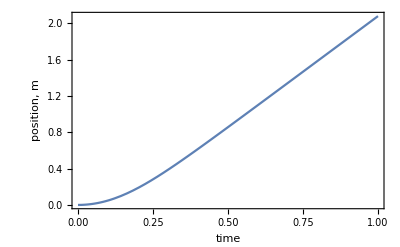

```mathematica
Plot[x[t]/.soln,{t,0,tMax}, FrameLabel->{"time","position, m"}]
```

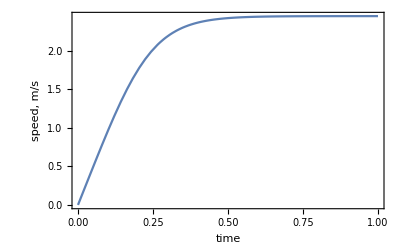

```mathematica
Plot[x'[t]/.soln,{t,0,tMax}, FrameLabel->{"time","speed, m/s"}]
```

## Figure 2.7

```mathematica
Remove["Global`*"]
```

```mathematica
SetOptions[Plot,Frame->True,Axes-> False,BaseStyle->{FontSize->16}];
```

```mathematica
b=0.2;c=0.2;m=1;g=9.8;
```

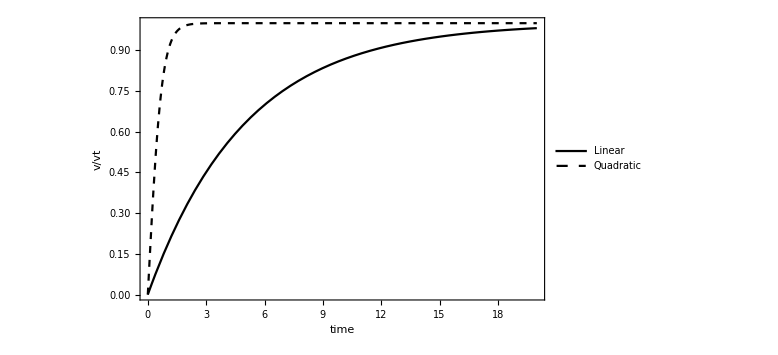

```mathematica
Plot[{1-Exp[-b t/ m],Tanh[c/m*Sqrt[m g/c]t]},{t,0,20},PlotStyle->{Black,{Black,Dashed}},FrameLabel->{"time","v/vt"},PlotLegends->Placed[{"Linear","Quadratic"},{Scaled[{0.5,0.3}], {0, 0.3}}]]
```